```mathematica
f=<|0->0,1->1|>; (* starting complexities map on generating set *)
Nrm=Norm; (* norm function *)
B=100; (* bound on norm *)

oldf=f;
Until[oldf==f,
oldf=f;
R=Keys[f];
For[i=1,i<=Length[R],i++,
If[¬MemberQ[R,-R[[i]]]||f[R[[i]]]+1<f[-R[[i]]],AssociateTo[f,-R[[i]]->f[R[[i]]]+1]];
For[j=1,j<=Length[R],j++,
sum=R[[i]]+R[[j]];
prod=R[[i]]*R[[j]];
If[(¬MemberQ[R,sum]&&Nrm[sum]<=B)||f[R[[i]]]+f[R[[j]]]<f[sum],AssociateTo[f,sum->f[R[[i]]]+f[R[[j]]]]];
If[(¬MemberQ[R,prod]&&Nrm[prod]<=B)||f[R[[i]]]+f[R[[j]]]<f[prod],AssociateTo[f,prod->f[R[[i]]]+f[R[[j]]]]];
]
];
]
```

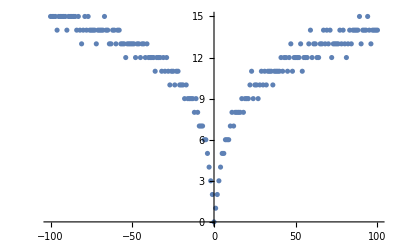

```mathematica
ListPlot[Sort[KeyValueMap[{#1,#2}&,f],#1[[1]]<#2[[1]]&]]
```

```mathematica
f=<|{{0,0},{0,0}}->0,{{1,0},{0,0}}->1,{{0,1},{0,0}}->1,{{0,0},{1,0}}->1,{{0,0},{0,1}}->1|>; (* starting complexities map on generating set *)
Remove[Nrm];
Nrm[m_]:=Total[Map[Abs,m,{2}],2]; (* norm function *)
B=6; (* bound on norm *)

oldf=f;
Until[oldf==f,
oldf=f;
R=Keys[f];
For[i=1,i<=Length[R],i++,
(*If[¬MemberQ[R,-R[[i]]]||f[R[[i]]]+1<f[-R[[i]]],AssociateTo[f,-R[[i]]->f[R[[i]]]+1]];*)
For[j=1,j<=Length[R],j++,
sum=R[[i]]+R[[j]];
prod=R[[i]].R[[j]];
If[(¬MemberQ[R,sum]&&Nrm[sum]<=B)||f[R[[i]]]+f[R[[j]]]<f[sum],AssociateTo[f,sum->f[R[[i]]]+f[R[[j]]]]];
If[(¬MemberQ[R,prod]&&Nrm[prod]<=B)||f[R[[i]]]+f[R[[j]]]<f[prod],AssociateTo[f,prod->f[R[[i]]]+f[R[[j]]]]];
]
];
]
DeleteCases[KeyValueMap[If[Nrm[#1]!=#2,{#1,#2}]&,f],Null]
```

{{{{6,0},{0,0}},5},{{{4,2},{0,0}},5},{{{2,4},{0,0}},5},{{{0,6},{0,0}},5},{{{4,0},{2,0}},5},{{{3,3},{0,0}},5},{{{3,0},{3,0}},5},{{{2,2},{1,1}},5},{{{2,1},{2,1}},5},{{{2,0},{4,0}},5},{{{1,2},{1,2}},5},{{{1,1},{2,2}},5},{{{0,3},{0,3}},5},{{{0,4},{0,2}},5},{{{0,2},{0,4}},5},{{{0,0},{6,0}},5},{{{0,0},{4,2}},5},{{{0,0},{2,4}},5},{{{0,0},{0,6}},5},{{{0,0},{3,3}},5}}